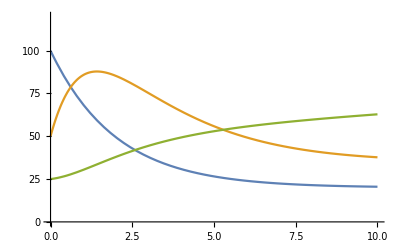

{{20.539},{37.7383},{62.8456}}

```mathematica
ClearAll["Global`*"]
(*NOTE: x*x ≠ xsq*)
(*0->M, M -> M + P, M -> 0, P -> 0,P+P->D*)
V=100;
c={0.1*V, 1, 0.5, 0.5, 0.1/V};
eqns={m'[t]==c[[1]]-c[[3]]m[t],
p'[t]==c[[2]]m[t]-c[[4]]p[t]-2*c[[5]]p[t]^2,
d'[t]==c[[5]]p[t]^2,
m[0]==V,p[0]==V/2,d[0]==V/4};
sol=NDSolve[eqns,{m,p,d},{t,0,10}];
Plot[{m[t]/.sol,p[t]/.sol,d[t]/.sol},{t,0,10},PlotRange->{0,V*1.2}]
N[{m[t]/.sol,p[t]/.sol,d[t]/.sol}/.{t->10},12]
```